```mathematica
Needs["MultivariateStatistics`"]
```

```mathematica
fGen:=Module[{offDiag=RandomReal[{-1,1}]},{{1,offDiag},{offDiag, 1}}]
```

```mathematica
fGen1:=Module[{offDiag12=RandomReal[{-1,1}],offDiag13=RandomReal[{-1,1}],offDiag23=RandomReal[{-1,1}],aMatrix},aMatrix={{1,offDiag12,offDiag13},{offDiag12, 1,offDiag23},{offDiag13,offDiag23,1}};If[PositiveDefiniteMatrixQ@aMatrix,aMatrix,fGen1]]
```

```mathematica
aList=Table[fGen1,{i,1,1000000}];
```

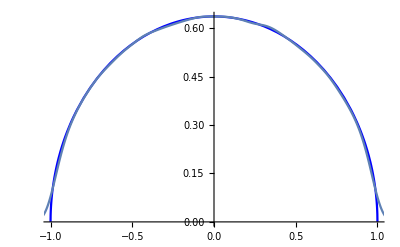

```mathematica
Show[Plot[PDF[TransformedDistribution[2 u -1,u\[Distributed]BetaDistribution[3/2,3/2]],x],{x,-1,1},PlotStyle->Blue] ,SmoothHistogram[aList[[All,1,2]]]]
```

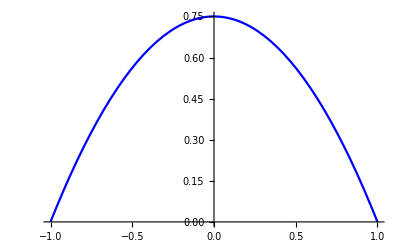

```mathematica
Show[Plot[PDF[TransformedDistribution[2 u -1,u\[Distributed]BetaDistribution[2,2]],x],{x,-1,1},PlotStyle->Blue] ]
```

```mathematica
n
```

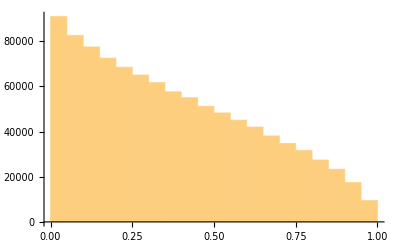

```mathematica
Histogram[Det/@aList]
```

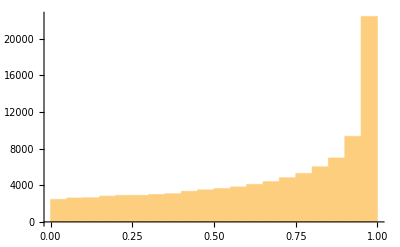

```mathematica
bList = Table[fGen,{i,1,100000}];
Histogram[Det/@bList]
```

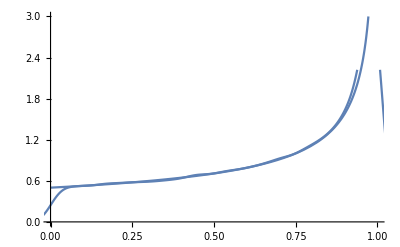

```mathematica
Show[Plot[PDF[BetaDistribution[1,1/2],x],{x,0,1},PlotRange->{Full,{0,3}}],SmoothHistogram[Det/@bList]]
```

```mathematica
Plot[PDF[TransformedDistribution[u v, {u\[Distributed]BetaDistribution[1,1],v\[Distributed]BetaDistribution[3/2,1/2]}],x],{x,0,1},PerformanceGoal->"Speed"]
```

$Aborted

```mathematica
PDF[TransformedDistribution[u v, {u\[Distributed]BetaDistribution[1,1],v\[Distributed]BetaDistribution[3/2,1/2]}],0.5]
```

1.

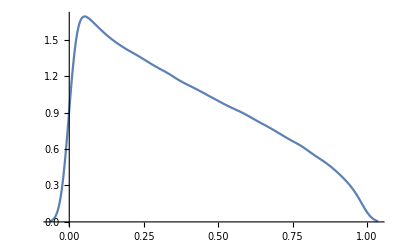

```mathematica
SmoothHistogram[RandomVariate[BetaDistribution[1,1],{1000000}]* RandomVariate[BetaDistribution[3/2,1/2],{1000000}]]
```

```mathematica
Clear[u]
```

```mathematica
tpdf=PDF[TransformedDistribution[u v,{u\[Distributed]BetaDistribution[1,1],v\[Distributed]BetaDistribution[3/2,1/2]}],x]
```

Piecewise[{{Indeterminate, x==0}, {(-(2 √x)/(√(1-x))+(2 x)/(√(-(-1+x) x))+4 ArcCos[√x])/π, 0<x<1}, {0, True}}]

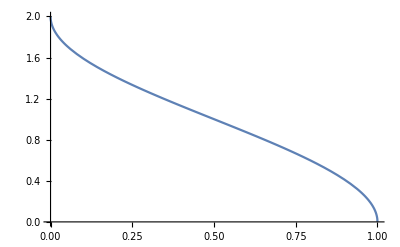

```mathematica
Plot[tpdf,{x,0,1}]
```

```mathematica
fTwoDimLKJ[η_]:=TransformedDistribution[u^η,u\[Distributed]BetaDistribution[1,1/2]]
```

```mathematica
aPDF=PDF[fTwoDimLKJ[1],x]
```

Piecewise[{{1/(2 √(1-x)), 0<x<1}, {0, True}}]

```mathematica
tpdf=PDF[TransformedDistribution[u v,{u\[Distributed]BetaDistribution[1,1],v\[Distributed]BetaDistribution[3/2,1/2]}],x]
```

Piecewise[{{Indeterminate, x==0}, {(-(2 √x)/(√(1-x))+(2 x)/(√(-(-1+x) x))+4 ArcCos[√x])/π, 0<x<1}, {0, True}}]

```mathematica
Plot[tpdf,{x,0,1}]
```

-Graphics-

```mathematica
vpdf=Convolve[aPDF,x^1,x,y]
```

-2/3+y

```mathematica
(1/Integrate[tpdf*x^2,{x,0,1}])
```

24/5

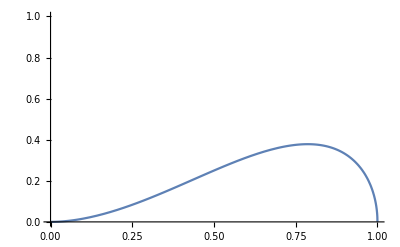

```mathematica
Plot[tpdf*x^2,{x,0,1},PlotRange->{Full,{0,1}}]
```

```mathematica
fPlotter[η_]:=Module[{aDenominator = Integrate[tpdf*x^η,{x,0,1}]},Plot[(1/aDenominator)* tpdf*x^η,{x,0,1}]]
```

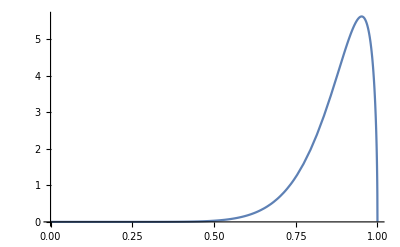

```mathematica
fPlotter[10]
```

```mathematica
fPDF[η_]:=PDF[TransformedDistribution[u v,{u\[Distributed]BetaDistribution[η,1],v\[Distributed]BetaDistribution[η+(1/2),1/2]}],x]
```

```mathematica
bPDF = fPDF[1]
cPDF = fPDF[2]
dPDF = fPDF[10]
```

Piecewise[{{Indeterminate, x==0}, {(-(2 √x)/(√(1-x))+(2 x)/(√(-(-1+x) x))+4 ArcCos[√x])/π, 0<x<1}, {0, True}}]

Piecewise[{{(2 x (-(4 √x)/(√(1-x))+3/(√(-(-1+x) x))-(3 x)/(√(-(-1+x) x^3))+(4 x^2)/(√(-(-1+x) x^3))+16 ArcCos[√x]))/(3 π), 0<x<1}, {0, True}}]

Piecewise[{{-1/(14549535 π)2 ((41287680 x^(19/2))/(√(1-x))-14549535/(2 √(-(-1+x) x))+(14549535 (1-2 x))/(2 √(-(-1+x) x))-(4849845 x^2 (-3+4 x))/(√(-(-1+x) x^3))-(3879876 x^4 (-5+6 x))/(√(-(-1+x) x^5))-(3325608 x^6 (-7+8 x))/(√(-(-1+x) x^7))-(2956096 x^8 (-9+10 x))/(√(-(-1+x) x^9))-(2687360 x^10 (-11+12 x))/(√(-(-1+x) x^11))-(2480640 x^12 (-13+14 x))/(√(-(-1+x) x^13))-(2315264 x^14 (-15+16 x))/(√(-(-1+x) x^15))-(2179072 x^16 (-17+18 x))/(√(-(-1+x) x^17))-(2064384 x^18 (-19+20 x))/(√(-(-1+x) x^19))-825753600 x^9 ArcCos[√x]), 0<x<1}, {0, True}}]

```mathematica
ePDF = fPDF[0.5]
```

Piecewise[{{Indeterminate, x==0}, {1/2 (-1/(√(1-x))+1./(√(1.-1. x))+ArcCos[√x]/(√x)), 0<x<1}, {0, True}}]

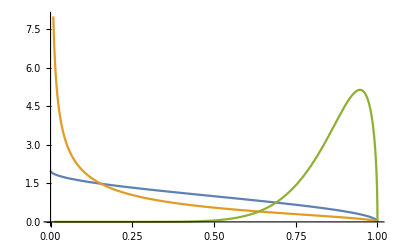

```mathematica
Plot[{bPDF,ePDF,dPDF},{x,0,1},PlotRange->{Full,{0,8}}]
```

```mathematica
fGen2:=Module[{offDiag12=0,offDiag13=0,offDiag23=RandomReal[{-1,1}],aMatrix},aMatrix={{1,offDiag12,offDiag13},{offDiag12, 1,offDiag23},{offDiag13,offDiag23,1}};If[PositiveDefiniteMatrixQ@aMatrix,aMatrix,fGen1]]
```

```mathematica
aList=Table[fGen2,{i,1,100000}]//Timing
```

{1.99681,{{{1,0,0},{0,1,-0.919902},{0,-0.919902,1}},{{1,0,0},{0,1,0.642937},{0,0.642937,1}},{{1,0,0},{0,1,-0.0841786},{0,-0.0841786,1}},{{1,0,0},{0,1,-0.73152},{0,-0.73152,1}},99993,{{1,0,0},{0,1,-0.856382},{0,-0.856382,1}},{{1,0,0},{0,1,-0.529102},{0,-0.529102,1}},{{1,0,0},{0,1,0.42914},{0,0.42914,1}}}}
 |  |  |  |

```mathematica
Det[{{1,b,c},{b,1,d},{c,d,1}}]
```

1-b^2-c^2+2 b c d-d^2